# Гауссовы пучки

Alexander Nekhaev

### Параметры системы:

```mathematica
l2=QuantityMagnitude[UnitConvert[Quantity[43.5,"Centimeters"]]];
l3=QuantityMagnitude[UnitConvert[Quantity[8,"Centimeters"]]];
f2=QuantityMagnitude[UnitConvert[Quantity[16.5,"Centimeters"]]];
λ=QuantityMagnitude[UnitConvert[Quantity[680,"Nanometers"]]];
(*ω0=;*)
ω=QuantityMagnitude[UnitConvert[Quantity[0.133,"Millimeters"]]];
```

Ищем:
f1, l1

### Функции для рассчетов:

```mathematica
(*Создаем пучок*)
InitBundle[R_,λ1_,ω1_]:=(q/.Solve[1/q==1/R-I λ1/(π ω1^2),q])[[1]];
(*Пропускаем пучок через систему*)
EvalBundle[OptMat_,qIn_]:=(OptMat[[1,1]]*qIn+OptMat[[1,2]])/(OptMat[[2,1]]*qIn+OptMat[[2,2]]);
(*Объединение матриц системы в одну матрицу*)
GroupOptics[Mats_]:=
Module[{i=0,res=0},
res=Mats[[Length[Mats]]];
For[i=Length[Mats]-1,i≥1,i--,
res=res.Mats[[i]];
];
 res
]
(*Создать матрицу тонкой линзы*)
ThinLense[f_]:=({{1, 0}, {-1/f, 1}});
(*Создать матрицу среды с постоянной*)
OpticSpace[d_,n_]:=({{1, d/n}, {0, 1}});
```

### Схема:

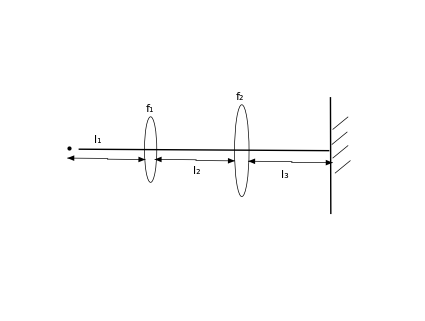

## Вычисления

Задаем элементы оптической системы:

```mathematica
system={
OpticSpace[l1,1],
ThinLense[f1],
OpticSpace[l2,1],
ThinLense[f2],
OpticSpace[l3,1]
};
```

Считаем матрицу системы :

```mathematica
systMat=GroupOptics[system];
systMat//MatrixForm
```

(0.515152-0.304091/f1 | 0.304091+(0.515152-0.304091/f1) l1
-6.06061+1.63636/f1 | -1.63636+(-6.06061+1.63636/f1) l1)

Запускаем пучок, выходящий из лазера:

```mathematica
q1=InitBundle[∞,λ,ω0]
```

25000000/17 ⅈ π ω0^2

Выходной пучок:

```mathematica
q3=InitBundle[∞,λ,ω]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.+0.081723 ⅈ

Считаем результат прохода пучка через систему:

```mathematica
l1v=(l1/.Solve[q3==Simplify[EvalBundle[systMat,q1]],{l1}])[[1]];
f1v=(f1/.Solve[q3==Simplify[EvalBundle[systMat,q1]],{f1}])[[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Simplify[Solve[{l1==l1v,f1==f1v},{l1,f1}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{l1→((-4.60679×10^37-2.30077×10^36 ⅈ)+(3.18818×10^52+5.84934×10^51 ⅈ) ω0^4-(0.117881-0.0608093 ⅈ) √((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4)+ω0^2 ((2.31503×10^44-1.9603×10^45 ⅈ)+(772716.-3.43951×10^6 ⅈ) √((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4)))/((2.4888×10^38+6.1835×10^37 ⅈ)-(5.50707×10^45-4.01558×10^45 ⅈ) ω0^2),f1→((-1.50355×10^38-8.732×10^37 ⅈ)+(1.36491×10^45+3.86934×10^45 ⅈ) ω0^2-0.5 √((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4))/((2.4888×10^38+6.1835×10^37 ⅈ)-(5.50707×10^45-4.01558×10^45 ⅈ) ω0^2)},{l1→((-4.60679×10^37-2.30077×10^36 ⅈ)+(3.18818×10^52+5.84934×10^51 ⅈ) ω0^4+(0.117881-0.0608093 ⅈ) √((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4)+ω0^2 ((2.31503×10^44-1.9603×10^45 ⅈ)-(772716.-3.43951×10^6 ⅈ) √((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4)))/((2.4888×10^38+6.1835×10^37 ⅈ)-(5.50707×10^45-4.01558×10^45 ⅈ) ω0^2),f1→(0.5 ((-3.00711×10^38-1.7464×10^38 ⅈ)+(2.72982×10^45+7.73867×10^45 ⅈ) ω0^2+√((5.99279×10^76+1.05032×10^77 ⅈ)-(1.32988×10^84+7.79707×10^84 ⅈ) ω0^2+(3.29772×10^91+3.0896×10^91 ⅈ) ω0^4)))/((2.4888×10^38+6.1835×10^37 ⅈ)-(5.50707×10^45-4.01558×10^45 ⅈ) ω0^2)}}